#### Trying to do the Plemelj integral for a Maxwellian dist, in §10.2 and just after equation (10.28) in Baumjohann and Treumann

```mathematica
maxFunc1Dvth=n0 (2 π)^(-1/2)vth Exp[-v^2/(2 vth^2)];
```

```mathematica
D[maxFunc1Dvth,v]
```

-(ⅇ^(-v^2/(2 vth^2)) n0 v)/(√(2 π) vth)

```mathematica
D[maxFunc1Dvth,v]/maxFunc1Dvth
```

-v/vth^2

Let a≡ω/k
Trying to do

```mathematica
indef=n0/((2 π)^(1/2) vth^3)Integrate[(v Exp[-v^2])/(v-a),{v,-∞,a-ϵ},Assumptions->a>0&&ϵ>0]
```

(n0 Integrate[(ⅇ^(-v^2) v)/(-a+v),{v,-∞,a-ϵ},Assumptions→a>0&&ϵ>0])/(√(2 π) vth^3)

```mathematica
bareIntegrand=(v Exp[-v^2])/(v-a);
```

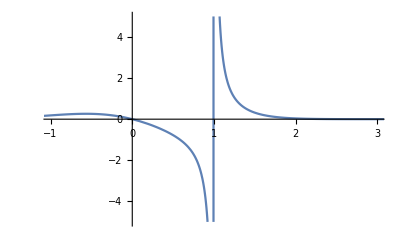

```mathematica
Plot[bareIntegrand/.a->1,{v,-10,10},PlotRange->{{-1,3},{-5,5}}]
```

Try transforming with variable w=v-a

```mathematica
indef2Coeff=n0/((2 π)^(1/2) vth^3);
```

```mathematica
indef2aIntegrand=Exp[-(w+a)^2/(2 vth^2)];
```

```mathematica
indef2bIntegrand=a/w Exp[-(w+a)^2/(2 vth^2)];
```

```mathematica
indef2Assump:=ϵ>0&&vth>0
```

```mathematica
indef2LB={w,-∞,-ϵ};
```

```mathematica
indef2UB={w,ϵ,∞};
```

```mathematica
indef2aLower=Integrate[ indef2aIntegrand,indef2LB,Assumptions->indef2Assump]
indef2aUpper=Integrate[ indef2aIntegrand,indef2UB,Assumptions->indef2Assump]
```

√(π/2) vth (1+Erf[(a-ϵ)/(√2 vth)])

√(π/2) vth Erfc[(a+ϵ)/(√2 vth)]

```mathematica
indef2aLower+indef2aUpper
```

```mathematica
√(π/2) vth (1+Erf[(a-ϵ)/(√2 vth)])+√(π/2) vth Erfc[(a+ϵ)/(√2 vth)]
```

```mathematica
indef2bLower=Integrate[ indef2bIntegrand,indef2LB,Assumptions->indef2Assump]
```

Integrate[(a ⅇ^(-(a+w)^2/(2 vth^2)))/w,{w,-∞,-ϵ},Assumptions→ϵ>0&&vth>0]

```mathematica
indef2bUpper=Integrate[ indef2bIntegrand,indef2UB,Assumptions->indef2Assump]
```

Integrate[(a ⅇ^(-(a+w)^2/(2 vth^2)))/w,{w,ϵ,∞},Assumptions→ϵ>0&&vth>0]

```mathematica
Integrate[1/w * ⅇ^(-(w^2+a^2-2w a)),{w,ϵ,∞},Assumptions->ϵ>0&&a>0]
```

Integrate[(ⅇ^(-a^2+2 a w-w^2))/w,{w,ϵ,∞},Assumptions→ϵ>0&&a>0]

```mathematica
Manipulate[Plot[1/w * ⅇ^(-(w^2+a^2-2w a))/.a->aVal,{w,-2,4}],{aVal,0,5,0.1}]
```

```mathematica
Limit[1/w * ⅇ^(-(w^2+a^2-2w a)),w->0,Direction->"FromBelow"]
```

DirectedInfinity[-ⅇ^(-ⅈ Im[a^2])]

```mathematica
Limit[1/w * ⅇ^(-(w^2+a^2-2w a)),w->0,Direction->"FromAbove"]
```

DirectedInfinity[ⅇ^(-ⅈ Im[a^2])]

```mathematica
Series[1/(v-a)^2,{v,a,4}]
```

1/(v-a)^2+O[v-a]^5